```mathematica
G = Exp[(-(DxIn-DxInCenter)^2)/(2 σ^2)]/(σ√(2 π))
```

(ⅇ^(-(DxIn-DxInCenter)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
(ⅇ^(-(-DxInCenter+DxIn)^2/(2 σ^2)))/(√(2 π) σ)
```

(ⅇ^(-(DxIn-DxInCenter)^2/(2 σ^2)))/(√(2 π) σ)

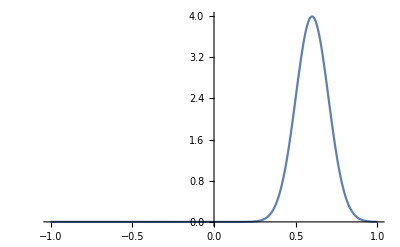

```mathematica
Plot[G/.σ->0.1/.DxInCenter->0.6,{DxIn,-1,1},PlotRange->Full]
```

```mathematica
DxOut=n1/n2 DxIn
```

(DxIn n1)/n2

```mathematica
DxInCrit=n2/n1
```

n2/n1

```mathematica
cosθ1=√(1-DxIn^2)
cosθ2=√(1-DxOut^2)
```

√(1-DxIn^2)

√(1-(DxIn^2 n1^2)/n2^2)

```mathematica
Rs=Abs[(n1*cosθ1-n2*cosθ2)/(n1*cosθ1+n2*cosθ2)]^2
```

Abs[(√(1-DxIn^2) n1-√(1-(DxIn^2 n1^2)/n2^2) n2)/(√(1-DxIn^2) n1+√(1-(DxIn^2 n1^2)/n2^2) n2)]^2

```mathematica
Rp=Abs[(n1*cosθ2-n2*cosθ1)/(n1*cosθ2+n2*cosθ1)]^2
```

Abs[(n1 √(1-(DxIn^2 n1^2)/n2^2)-√(1-DxIn^2) n2)/(n1 √(1-(DxIn^2 n1^2)/n2^2)+√(1-DxIn^2) n2)]^2

```mathematica
R=Simplify[(Rs+Rp)/2,Assumptions->{n2>=1,n1>n2,DxIn<1,DxIn>-1,n1∈Reals,n2∈Reals,DxIn∈Reals}]
```

1/2 (Abs[(√(1-DxIn^2) n1-√(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n1+√(-DxIn^2 n1^2+n2^2))]^2+Abs[(√(1-DxIn^2) n2^2-n1 √(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n2^2+n1 √(-DxIn^2 n1^2+n2^2))]^2)

```mathematica
T=1-R
```

1+1/2 (-Abs[(√(1-DxIn^2) n1-√(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n1+√(-DxIn^2 n1^2+n2^2))]^2-Abs[(√(1-DxIn^2) n2^2-n1 √(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n2^2+n1 √(-DxIn^2 n1^2+n2^2))]^2)

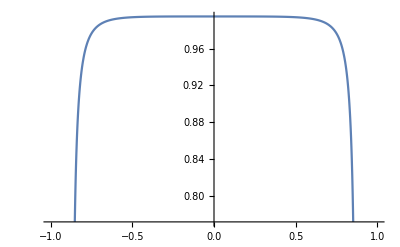

```mathematica
Plot[T/.{n1->1.5,n2->1.3},{DxIn,-1,1}]
```

```mathematica
Integrate[G,{DxIn,-∞,∞}, Assumptions->σ>0]
```

1

```mathematica
G*T
```

(ⅇ^(-(DxIn-DxInCenter)^2/(2 σ^2)) (1+1/2 (-Abs[(√(1-DxIn^2) n1-√(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n1+√(-DxIn^2 n1^2+n2^2))]^2-Abs[(√(1-DxIn^2) n2^2-n1 √(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n2^2+n1 √(-DxIn^2 n1^2+n2^2))]^2)))/(√(2 π) σ)

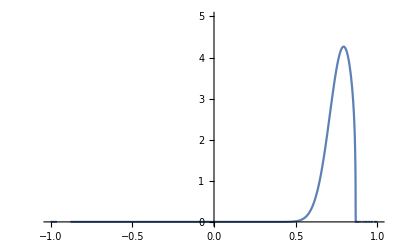

```mathematica
Plot[G*T/.{n1->1.5,n2->1.3,σ->0.089,DxInCenter->0.8},{DxIn,-1,1},PlotRange->{{-1,1},{0,5}}]
```

```mathematica
Int=Integrate[G*T,{DxIn,-DxInCrit,DxInCrit}, Assumptions->{n2>=1,n1>n2,n1∈Reals,n2∈Reals,DxIn∈Reals,σ>0}]
```

Integrate[(ⅇ^(-(DxIn-DxInCenter)^2/(2 σ^2)) (1+1/2 (-Abs[(√(1-DxIn^2) n1-√(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n1+√(-DxIn^2 n1^2+n2^2))]^2-Abs[(√(1-DxIn^2) n2^2-n1 √(-DxIn^2 n1^2+n2^2))/(√(1-DxIn^2) n2^2+n1 √(-DxIn^2 n1^2+n2^2))]^2)))/(√(2 π) σ),{DxIn,-n2/n1,n2/n1},Assumptions→{n2≥1,n1>n2,n1∈ℝ,n2∈ℝ,DxIn∈ℝ,σ>0}]

```mathematica
Plot[Int/.{σ->0.089,n1->1.5,n2->1.3},{DxInCenter,-1,1}, PlotRange->{{-1,1},{0,1}}]
```

$Aborted

```mathematica
DxEff=Simplify[n1/n2 1/Int Integrate[DxIn*G*T,{DxIn,-DxInCrit,DxInCrit}, Assumptions->{σ>0,DxInCrit>0}]]
```

0

```mathematica
Plot[DxEff/.σ->0.0892/.DxInCrit->1.3/1.5/.n1->1.5/.n2->1.3,{DxInCenter,-1,1}, PlotRange->All]
```

$Aborted